```mathematica
Clear["Global`*"]
```

## Compare diffusion lengths

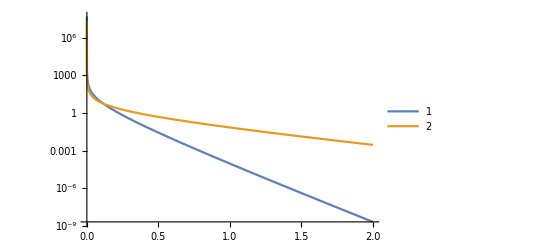

```mathematica
f[r_,λ_]:= λ/r Exp[(R-r)/λ]/. {R-> 0.3};
λvals ={λα->0.1, λβ-> 0.4};
LogPlot[{f[r,λα]/.λvals,f[r,λβ]/.λvals}, {r,0,2}, PlotLegends-> Automatic, PlotRange-> All]
```

```mathematica
N[f[r,λα]/f[r,λβ]/.λvals/. {r-> 0}]
```

1.0585

Plot region where f[r,λα]/f[r,λβ]|_(r→ 0) >  1
If λ_α < λ_β, then we want f[r,λα]/f[r,λβ]|_(r→ 0) >  1 => White region above diagonal
If λ_α > λ_β, then we want f[r,λα]/f[r,λβ]|_(r→ 0) <  1 => Black region below diagonal

```mathematica
λαrange= Range[0.1,2,0.1];
λβrange= Range[0.1,2,0.1];
vals = Table[f[r,λα]/f[r,λβ]/. {r-> 0}, {λα,0.1, 5, 0.1}, {λβ,0.1,5, 0.1}];
valsBoolean = Table[Boole[(f[r,λα]/f[r,λβ]/. {r-> 0})>1], {λα,λαrange[[1]],λαrange[[-1]],  λαrange[[2]]-λαrange[[1]]}, {λβ,λβrange[[1]],λβrange[[-1]],  λβrange[[2]]-λβrange[[1]]}];
yticks = Table[{i, λαrange[[i]]}, {i,5, Length[λαrange], 5} ];
xticks = Table[{i, λβrange[[i]]}, {i,5, Length[λβrange], 5} ];
ArrayPlot[valsBoolean, Mesh-> None, PlotLegends->Automatic, FrameLabel-> {"λ_α", "λ_β"}, DataReversed->True, FrameTicks-> {yticks, xticks}]
```

-Graphics-

Try to solve inequality
=> Not feasible

```mathematica
Reduce[{α/β Exp[2/α-2/β]<1 && α<β}]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

```mathematica
Plot3D[(α/β Exp[R/α-R/β]/. {R-> 1}), {α,0,1}, {β,0,1}]
```

-Graphics3D-

```mathematica
Solve[α/β Exp[R/α-R/β] == 1, {α}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-R/ProductLog[-(ⅇ^(-R/β) R)/β]}}